## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
```

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
(*Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])*)
```

# N = 3, without V3

```mathematica
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]);
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2-(7 λ)/12,-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2-(7 λ)/12,-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2-λ/4}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-3/2-λ/4 | -χ/(2 √3) | -λ/(2 √3) | 0
-χ/(2 √3) | -1/2-(7 λ)/12 | -χ | -λ/(2 √3)
-λ/(2 √3) | -χ | 1/2-(7 λ)/12 | -(5 χ)/(2 √3)
0 | -λ/(2 √3) | -(5 χ)/(2 √3) | 3/2-λ/4)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies and eigenvalues

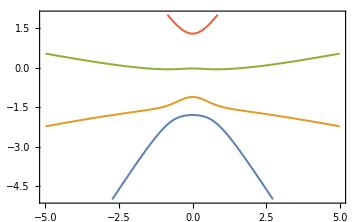
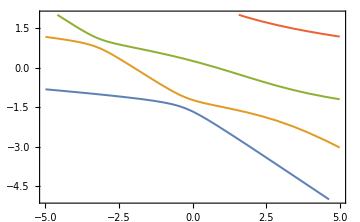

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->MaTeX/@{"E_0","E_1","E_2","E_3"},PlotPoints->20,PlotRange->{Automatic,{-5,2}},Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->Thickness[0.004]};
{plA,plB}={Plot[energies1,{χ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\chi","Energy"}],
Plot[energies2,{λ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","Energy"}]}
```

```mathematica
en[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
```

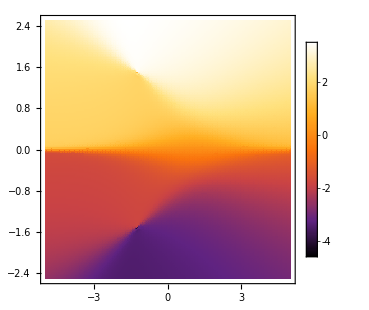

```mathematica
points=
enDifPlot=DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-5,5},{χ,-2.5,2.5},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310]
```

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-4,4},{χ,-2,2},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->50];
```

### Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solMultileft=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,15},PrecisionGoal->2,AccuracyGoal->2],{i,0,2π,0.3}];
```

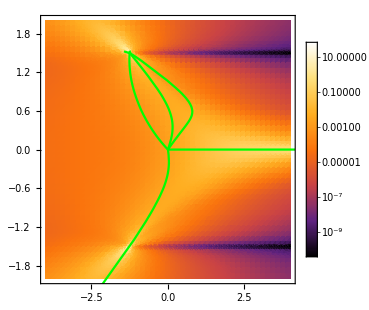

```mathematica
pl1=ParametricPlot[{λ[t],χ[t]}/.solMultileft,{t,0,15},PlotRange->All,Frame->True,PlotStyle->Green];
plt=Show[{geodbg,pl1}, ImageSize->310]
```

## Analytical solution

```mathematica
Eigenvalues[
```

# N = 3, without V2

has no point, its just a mess with huge along - axes values

# N = 3, only tridiagonal

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m]);
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),0,0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,0},{0,-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,0,-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(1/4 (-6-λ) | -χ/(2 √3) | 0 | 0
-χ/(2 √3) | 1/12 (-6-7 λ-4 χ^2) | -χ | 0
0 | -χ | 1/12 (6-7 λ-16 χ^2) | -(5 χ)/(2 √3)
0 | 0 | -(5 χ)/(2 √3) | 3/2-λ/4-3 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies and eigenvalues

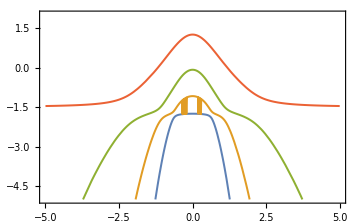
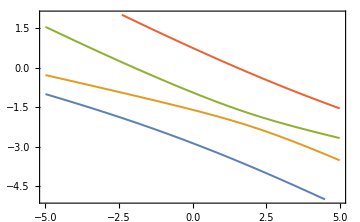

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->MaTeX/@{"E_0","E_1","E_2","E_3"},PlotPoints->20,PlotRange->{Automatic,{-5,2}},Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->Thickness[0.004]};
{plA,plB}={Plot[energies1,{χ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\chi","Energy"}],
Plot[energies2,{λ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","Energy"}]}
```

```mathematica
en[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
```

```mathematica
points=
enDifPlot=DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-5,5},{χ,-2.5,2.5},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310]
```

-Graphics-

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

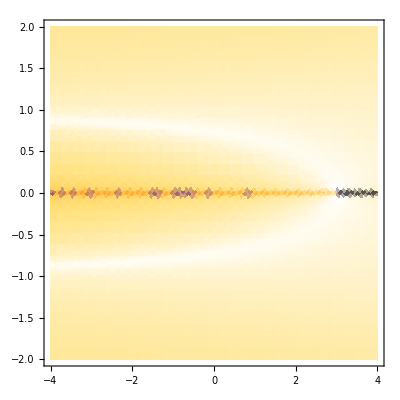

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-4,4},{χ,-2,2},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->30]
```

## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"}
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
```

{PerformanceGoal→Quality,PlotRange→Full,FrameLabel→{-Graphics-,-Graphics-},{BaseStyle→Directive[FontSize→12],AxesStyle→Directive[FontSize→12],TicksStyle→Directive[FontSize→12],LabelStyle→{FontFamily→Latin Modern Roman,FontSize→12},BaseStyle→texStyle},ColorFunction→SunsetColors}

# N = 3, cutting what can be cutted

χ^2 element causes leaning of singular line (to the right, making it horizontal). Removing V2 has no meaning, creates just two along-axex lines

So if V3 = 0 and δ[mp, m] (Je[-1, j, m] Je[1, j, m - 1] + Je[1, j, m] Je[-1, j, m + 1] ) from V1 is removed, and 1/2(m+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]+ from V2 is removed

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2])
V2[jp_,mp_,j_,m_]:=1/2(m+j)Je[-1,j,m]δ[mp,m-1]+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]);
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2,-(2 χ)/3,-λ/(2 √3)},{-λ/(2 √3),-(2 χ)/3,1/2,-(√3 χ)/2},{0,-λ/(2 √3),-(√3 χ)/2,3/2}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-3/2 | -χ/(2 √3) | -λ/(2 √3) | 0
-χ/(2 √3) | -1/2 | -(2 χ)/3 | -λ/(2 √3)
-λ/(2 √3) | -(2 χ)/3 | 1/2 | -(√3 χ)/2
0 | -λ/(2 √3) | -(√3 χ)/2 | 3/2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
Plot3D[gC[λ,χ],{λ,-5,5},{χ,0,5},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

## Energies and eigenvalues

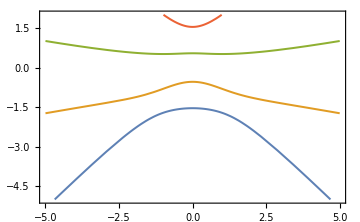
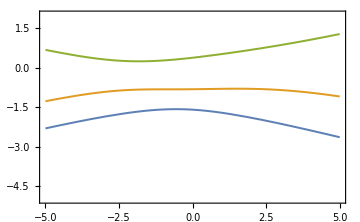

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->MaTeX/@{"E_0","E_1","E_2","E_3"},PlotPoints->20,PlotRange->{Automatic,{-5,2}},Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->Thickness[0.004]};
{plA,plB}={Plot[energies1,{χ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\chi","Energy"}],
Plot[energies2,{λ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","Energy"}]}
```

```mathematica
en[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
```

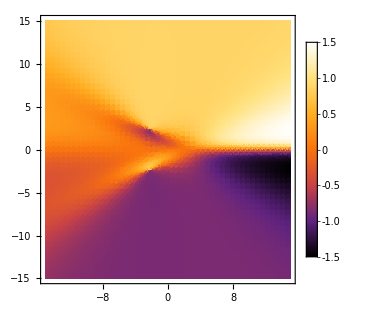

```mathematica
points=
enDifPlot=DensityPlot[(#⟦2⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-15,15},{χ,-15,15},Evaluate@densityPlotOptions,PlotPoints->50, ImageSize->310]
```

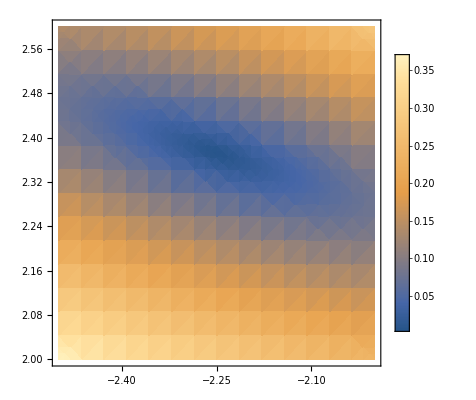

```mathematica
DensityPlot[en[λ,χ]⟦2⟧-en[λ,χ]⟦1⟧,{λ,-2.5,-2},{χ,2,2.6},PlotLegends->Automatic]
```

## Energies and eigenvectors analytically

```mathematica
AG[λ_,χ_]:=(45+3 λ^2+23 χ^2) 
AA[λ_,χ_]:=(-16 AG[λ,χ]^3+248832 (-3 χ^2+λ χ^2)^2+1296 AG[λ,χ](81+18 λ^2+λ^4+54 χ^2+48 λ χ^2-6 λ^2 χ^2+9 χ^4)+√(-4 (16848+3024 λ^2+144 λ^4+14112 χ^2+5184 λ χ^2-96 λ^2 χ^2+3088 χ^4)^3+(-16 AG[λ,χ]^3+248832 (-3 χ^2+λ χ^2)^2+1296 AG[λ,χ](81+18 λ^2+λ^4+54 χ^2+48 λ χ^2-6 λ^2 χ^2+9 χ^4))^2))^(1/3);
AB[λ_,χ_]:=(192 (-3 χ^2+λ χ^2))/(√AD[λ,χ]);
AC[λ_,χ_]:=(16 2^(1/3) (1053+189 λ^2+9 λ^4+882 χ^2+324 λ χ^2-6 λ^2 χ^2+193 χ^4));
AD[λ_,χ_]:=(4/3 AG[λ,χ]+AC[λ,χ]/(3 AA[λ,χ])+1/(3 2^(1/3))AA[λ,χ]);
AAA[λ_,χ_]:=8/3 AG[λ,χ]-AC[λ,χ]/(3 AA[λ,χ])-1/(3 2^(1/3))AA[λ,χ]
```

```mathematica
enA[λ_,χ_]:={1/6 (-1/2 √AD[λ,χ]-1/2 √(AAA[λ,χ]+AB[λ,χ])),
1/6 (-1/2 √AD[λ,χ]+1/2 √(AAA[λ,χ]+AB[λ,χ])),
1/6 (1/2 √AD[λ,χ]-1/2 √(AAA[λ,χ]-AB[λ,χ])),
1/6 (1/2 √AD[λ,χ]+1/2 √(AAA[λ,χ]-AB[λ,χ]))};
```

```mathematica
N@enA[1,1]
```

{-1.71535-6.06979×10^-17 ⅈ,-0.80589+1.29197×10^-16 ⅈ,0.51273-9.19788×10^-17 ⅈ,2.00851+2.34802×10^-17 ⅈ}

```mathematica
Solve[AAA[λ,χ]+AB[λ,χ]==0,{λ,χ}]
```

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

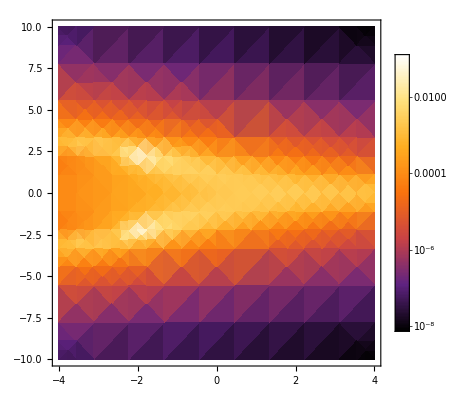

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-4,4},{χ,-10,10},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->10]
```

### Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solMultileft=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,7},PrecisionGoal->3,AccuracyGoal->3],{i,0,π,0.1}];
```

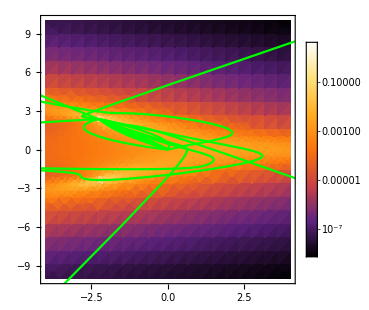

```mathematica
pl1=ParametricPlot[{λ[t],χ[t]}/.solMultileft,{t,0,15},PlotRange->All,Frame->True,PlotStyle->Green];
plt=Show[{geodbg,pl1}, ImageSize->310]
```

# GRQuick

```mathematica
<<GRQUICKv4.m
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ],Quartics->True];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ],Quartics->True]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]//FullSimplify
```

```mathematica
Metin[g[λ,χ],{λ,χ}]
```

```mathematica
H[λ,χ]
```

H[λ,χ]